```mathematica
∑_(k=1)^n (a+k*(b-a)/n)
```

```mathematica
1/2 (-a+b+a n+b n)//FullSimplify
```

1/2 (-a+b+(a+b) n)

```mathematica
∑_(i=1)^n (a+i*(b-a)/n)((a+i*(b-a)/n)-(a+(i-1)*(b-a)/n))
```

```mathematica
-((a-b) (-a+b+a n+b n))/(2 n)//FullSimplify
```

-((a-b) (-a+b+(a+b) n))/(2 n)

```mathematica
∑_(i=1)^n (a+(i-1)*(b-a)/n)((a+i*(b-a)/n)-(a+(i-1)*(b-a)/n))
```

(-a^2+2 a b-b^2-a^2 n+b^2 n)/(2 n)

```mathematica
(-a^2+2 a b-b^2-a^2 n+b^2 n)/(2 n)//FullSimplify
```

-((a-b) (a-b+(a+b) n))/(2 n)

```mathematica
?Limit
```

Limit[expr,x->x_0] finds the limiting value of expr when x approaches x_0.

```mathematica
Limit[-((a-b) (-a+b+(a+b) n))/(2 n),n->Infinity]
```

-1/2 (a-b) (a+b)

```mathematica
f[x_]:=Sqrt[1-x^2]
```

```mathematica
D[f,x]
```

0

```mathematica
D[f[x],x]
```

-x/(√(1-x^2))

```mathematica
?D
```

D[f,x] gives the partial derivative ∂f/∂x. 
D[f,{x,n}] gives the multiple derivative ∂^n f/∂x^n. 
D[f,x,y,…] differentiates f successively with respect to x,y,….
D[f,{{x_1,x_2,…}}] for a scalar f gives the vector derivative (∂f/∂x_1,∂f/∂x_2,…). 
D[f,{array}] gives a tensor derivative.

```mathematica
Integrate[Sqrt[1-(x/(1-x^2))^2],x]
```

∫√(1-x^2/((1-x^2)^2))ⅆx

```mathematica
Integrate[Sqrt[1+D[f[x],x]^2],{x,-1/2,1/2}]
```

π/3

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

```mathematica
ArcSin[1/2]-ArcSin[-1/2]
```

π/3

```mathematica
2 ArcTan[1/2]//
```

0.927295

```mathematica
Pi/3//N
```

1.0472

```mathematica
Integrate[Sqrt[2],{x,0,1}]
```

√2

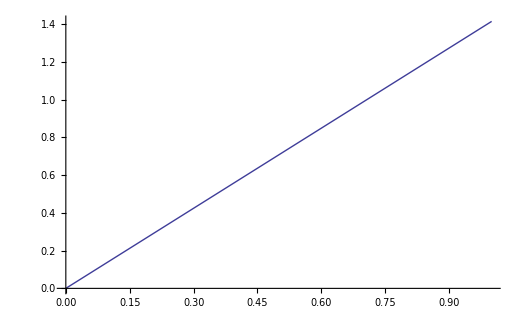

```mathematica
Plot[Sqrt[2]x,{x,0,1}]
```

```mathematica
Integrate[1/(x+1)+1/x^2,{x,2,10}]
```

2/5+Log[11/3]

```mathematica
Integrate[Exp[Sin[x]]Cos[x],{x,0,2π}]
```

0

```mathematica
Sin[2π]
```

0

```mathematica
Integrate[Cos[x]Cos[2x],{x,0,2π}]
```

0

```mathematica
Integrate[Cos[2x],x]
```

1/2 Sin[2 x]

```mathematica
?Integrate
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f.

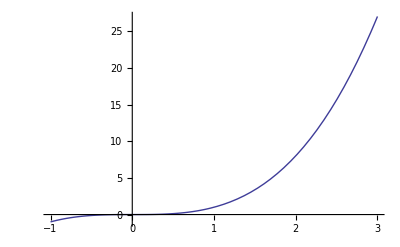

```mathematica
Plot[x^3,{x,-1,3}]
```

```mathematica
g[x_]:=1
```

```mathematica
∫xⅆg[x]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1.

∫xⅆ1

```mathematica
Integrate[x,1]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1.

∫xⅆ1

```mathematica
f[x_]:=x
```

```mathematica
Integrate[f[x],g[x]]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1.

∫xⅆ1

```mathematica
Integrate[3x^3,{x,-1,3}]
```

60

```mathematica
(3/4)3^4
```

243/4

```mathematica
3/4(-1)^4
```

3/4

```mathematica
f[x_]:=Cos[x]1/2Sin[2x]+2(-1/2Sin[x]Cos[2x])
```

```mathematica
f[2π]
```

0

```mathematica
f[0]
```

0

```mathematica
GCD[112,1113]
```

7

```mathematica
?Tupel
```

Information::notfound: Symbol "Tupel" not found.

```mathematica
?Tuple
```

Information::notfound: Symbol "Tuple" not found.

```mathematica
?Permutation
```

Information::notfound: Symbol "Permutation" not found.

```mathematica
Subsets[Subsets[{1,2}]]
```

{{},{{}},{{1}},{{2}},{{1,2}},{{},{1}},{{},{2}},{{},{1,2}},{{1},{2}},{{1},{1,2}},{{2},{1,2}},{{},{1},{2}},{{},{1},{1,2}},{{},{2},{1,2}},{{1},{2},{1,2}},{{},{1},{2},{1,2}}}

```mathematica
Subsets[Subsets[{}]]
```

{{},{{}}}